## Visualisation:

```mathematica
Manipulate[
ArrayPlot[Table[If[RandomReal[] > p, 0,1],2 ^ size,2 ^ size]],
{{p, 0.5},0,1,0.05},
{{size, 4}, 1, 6, 1}]
```

## Function Definitions:

```mathematica
generate2d[size_,p_] := Table[If[RandomReal[] > p, 0,1],2 ^ size,2 ^ size];
compress2D[{a_,b_},{c_,d_}]:=If[(a==1&&c==1)||(b==1&&d==1),1,0]
```

```mathematica
renormOnce2D[array_] := Table[
compress2D[{array⟦i⟧⟦j⟧,array⟦i⟧⟦j+1⟧},{array⟦i+1⟧⟦j⟧,array⟦i+1⟧⟦j+1⟧}],
{i,1,Length[array],2},{j,1,Length[array],2}
]
renorm2d[array_] := Nest[renormOnce2D,array,Log[2,Length[array]]]
renorm2dAverage[size_,p_, number_] := Mean[
Table[renorm2d[generate2d[size,p]]⟦1⟧⟦1⟧,{number}]
]
```

## Renormalization group visualization:

```mathematica
size := 6
p := 0.6
imgList = {};
grid = generate2d[size,p];
Do[imgList = Append[imgList,Image[ ArrayPlot[Nest[renormOnce2D,grid,n]]]],{n,0,size}]
ImageCollage[imgList]
```

-Graphics-

## Percolation function:

```mathematica
size1 = 3;(* 2^3 = 8*)
Timing[data1 = Table[renorm2dAverage[size1,p,500],{p,0,1,0.05}]]
```

{1.99922,{0,0,0,0,0,0,1/100,3/250,13/250,16/125,59/250,101/250,139/250,181/250,87/100,119/125,99/100,1,1,1,1}}

```mathematica
size2 = 4;(* 2^4 = 16*)
Timing[data2 = Table[renorm2dAverage[size2,p,500],{p,0,1,0.05}]]
```

{7.45916,{0,0,0,0,0,0,0,0,1/125,9/250,29/250,131/500,58/125,379/500,233/250,99/100,1,1,1,1,1}}

```mathematica
size3 = 5; (* 2^5 = 32*)
Timing[data3 = Table[renorm2dAverage[size3,p,500],{p,0,1,0.05}]]
```

{28.7009,{0,0,0,0,0,0,0,0,0,0,3/100,17/125,64/125,217/250,247/250,1,1,1,1,1,1}}

```mathematica
size4 = 6; (* 2^6 = 64*)
Timing[data4 = Table[renorm2dAverage[size4,p,500],{p,0,1,0.05}]]
```

{114.647,{0,0,0,0,0,0,0,0,0,0,0,9/250,101/250,229/250,1,1,1,1,1,1,1}}

```mathematica
size5 = 7; (*2^7 = 128*)
listP = {0,0.1,0.2,0.3,0.4,0.5,0.55,0.6,0.65,0.7,0.8,0.9,1}
data5 = Table[renorm2dAverage[size5,p,500],{p,listP}]
```

{0,0.1,0.2,0.3,0.4,0.5,0.55,0.6,0.65,0.7,0.8,0.9,1}

{0,0,0,0,0,0,0,129/500,489/500,1,1,1,1}

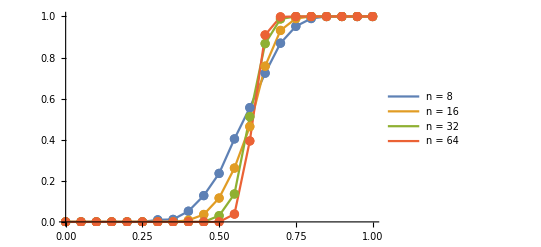

```mathematica
ListLinePlot[
{data1,data2,data3,data4},
Mesh->Full,DataRange->{0,1},
PlotLegends->{"n = 8","n = 16","n = 32","n = 64"}
]
```

```mathematica
Export["PercolationSize.xlsx",Transpose[{data1,data2,data3,data4}]]
```

PercolationSize.xlsx

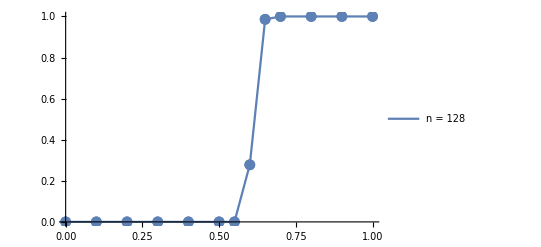

```mathematica
ListLinePlot[Partition[Riffle[listP,data5],2],Mesh->Full,DataRange->{0,1},PlotLegends->{"n = 128"}]
```

```mathematica
Export["Percolation128.xlsx",Column[data5]]
```

Percolation128.xlsx